# Impact of Parameter Perturbation on the Neural Network Performance

This project investigates the impact of perturbing parameters of a trained neural network on its performance by adding random noise to each layer. My project addresses the big question: “How resilient are neural network to perturbations or noise?” This question has an interesting implication for running neural networks where energy and computational resources are limited. 

<<RESULTS & CONCLUSION>>

## Table of Contents

Introduction

The LeNet Model

The MNIST Dataset

Exploratory Data Analysis

Extracting the Weights from LeNet

Summary Statistics of Weight Distribution

Adding Noise to

## 1. Introduction

## 1.1 The LeNet Model

LeNet Model is a convolutional neural network for image classification developed by Yann LeCun and his collaborators at AT&T Bell Labs. Trained on the MNIST dataset, it is known to have achieved a significantly high performance in classifying handwritten digits with an error rate less than 1% per digit.1

```mathematica
leNet = NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<11>]

#### Architecture

LeNet comprises two main parts: the two convolutional layers and the two fully connected layers. The LeNet takes an image of handwritten digit of size  and pass it through the convolutional layers with max pooling to extract its features, which results in a feature map of dimensions . Then, it flattens the feature map into a column vector of size  and then pass it through the fully connected layers to classify it. Below are the summary graphics showing the architecture of the LeNet.

```mathematica
Information[leNet,"FullSummaryGraphic"]
```

-Graphics-

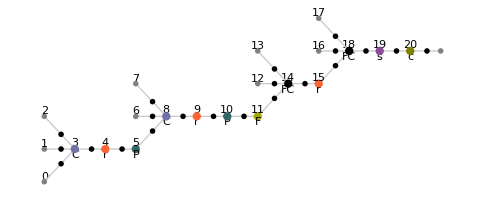

```mathematica
Information[ NetModel["LeNet Trained on MNIST Data"],"MXNetNodeGraphPlot"]
```

## 1.2 The MNIST Dataset

The LeNet is was trained on the MNIST dataset of handwritten digits and is known to have achieved 98.5% accuracy on the MNIST test dataset. The data points are in pairs of  image and labels of digits between 0 and 9. The MNIST database consists of a training set of 60,000 examples and a test set of 10,000 examples.2

```mathematica
mnistTest = ResourceData["MNIST","TestData"];
```

## 2. Exploratory Data Analysis: Weight Distribution

## 2.1 Extracting the Weights

We extract the weights from the LeNet for each layer. The 1st (Convolutional), 4th (Convolutional), 8th (Linear) and 10th (Linear) layers have weights.

```mathematica
layerWeights = Table[NetExtract[leNet, {n, "Weights"}], {n, {1, 4, 8, 10}}]
```

{NumericArray[…],NumericArray[…],NumericArray[<500,800>, Real32],NumericArray[…]}

## 2.2 Summary Statistics

Center: All layers have means and medians close to 0, which indicate that the data centered around zero with slight deviations.

Shape: As we can see from the histograms and the coefficient of skewness, the weight distributions are not symmetrical. Layer 1 (-0.457827) and 4 (-0.463588) are approximately symmetrical but slightly left-skewed shape with moderately small, negatives coefficients of skewness. On the other hand, layer 8 (-1.44888) and 10 (-0.769615)  are more left-skewed than the first two with a greater magnitude of skewness coefficient In particular, layer 8 is highly left-skewed with a coefficient significantly less than 1.  While the mean and the median of each distribution are fairly close to each other, the mean is slightly less than its median for each distribution. This is likely the result of the slight left skewness, as the extreme values pull the mean to the left side.

Spread: Layer 1 has the highest range (3.87316), which means it has the most variability overall. This is likely influenced by its skewness and the extreme values. The other three layers have fairly similar ranges. Considering the skewness of the distributions, we could use IQR to measure the variability of the data distributions. Layer 1 (0.457827) has the highest IQR, which means it has the greatest central variability.

### Graphical Summary

We can plot the box plot and histogram of the weights distribution for each layer and visually analyze the center, spread, and shape of the distributions.

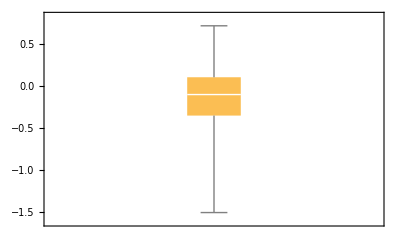
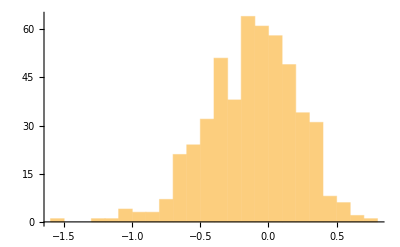
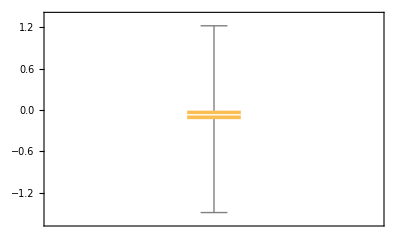
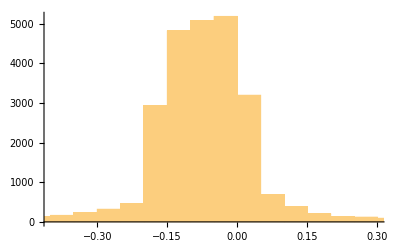
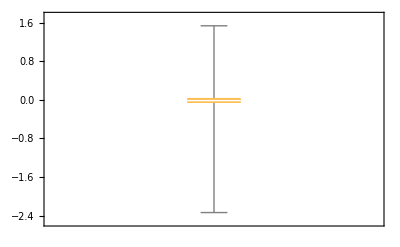
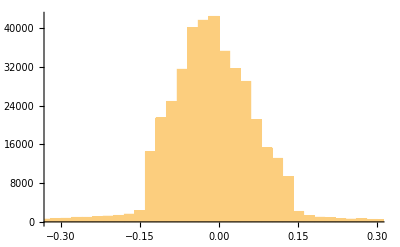
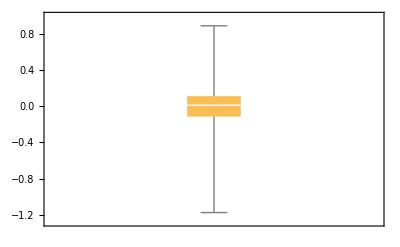
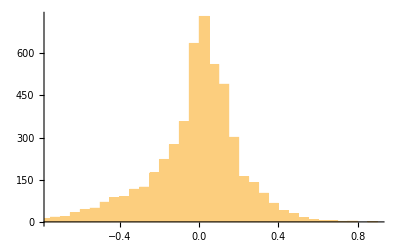
Weights Distribution
Layer 1
(Convolutional) | -Graphics- | -Graphics-
Layer 4
(Convolutional) | -Graphics- | -Graphics-
Layer 8
(Linear) | -Graphics- | -Graphics-
Layer 10
(Linear) | -Graphics- | -Graphics-

```mathematica
Grid[
{
{Style["Weights Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Table[{BoxWhiskerChart[Flatten[layerWeights[[l]]//Normal]],Histogram[Flatten[layerWeights[[l]]//Normal]]},{l,1,4}],
	TableHeadings->{{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}]}
},
Spacings->{2,1}
]
```

### Numerical Summary

The following are the numerical summary of the weights distribution that summarizes the distribution of the weights with numerical measures.

```mathematica
Grid[
{{Style["Weights Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Transpose[Table[
{
Mean[Flatten[layerWeights[[l]]//Normal]],
StandardDeviation[Flatten[layerWeights[[l]]//Normal]],
Min[Flatten[layerWeights[[l]]//Normal]],
Quartiles[Flatten[layerWeights[[l]]//Normal]][[1]],
Median[Flatten[layerWeights[[l]]//Normal]],
Quartiles[Flatten[layerWeights[[l]]//Normal]][[3]],
Max[Flatten[layerWeights[[l]]//Normal]],
(Max[Flatten[layerWeights[[l]]//Normal]]-Min[Flatten[layerWeights[[l]]//Normal]]),
InterquartileRange[Flatten[layerWeights[[l]]//Normal]],
Skewness[Flatten[layerWeights[[l]]//Normal]]
},
{l,1,4}
]],
TableHeadings->{{"Mean","Standard Deviation","Min","Q1/4","Median","Q3/4","Max","Range","IQR","Skewness"},{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}
]}},
Spacings->{2,1}
]
```

Weights Distribution
 | Layer 1
(Convolutional) | Layer 4
(Convolutional) | Layer 8
(Linear) | Layer 10
(Linear)
Mean | -0.1234 | -0.075064 | -0.0162563 | -0.019502
Standard Deviation | 0.332887 | 0.150124 | 0.117813 | 0.226538
Min | -1.5101 | -1.49051 | -2.33753 | -1.17305
Q1/4 | -0.351734 | -0.134291 | -0.0650547 | -0.115114
Median | -0.10042 | -0.0711243 | -0.0159563 | 0.0103053
Q3/4 | 0.106093 | -0.0109469 | 0.0396426 | 0.110383
Max | 0.720769 | 1.22129 | 1.53562 | 0.885933
Range | 2.23087 | 2.7118 | 3.87316 | 2.05898
IQR | 0.457827 | 0.123344 | 0.104697 | 0.225497
Skewness | -0.445425 | -0.463588 | -1.44888 | -0.769615

## 3. Methodology

The four layers in LeNet that have weights are the 1st convolutional layer, the 4th convolutional layer , the 8th linear layer, the 10th linear layer. This experiment assesses the neural network’s sensitivity to perturbations by varying the noise range and the specific layers to which the random noise is added. By randomly sampling noise from various distributions (uniform and Gaussian) and perturbing each layer individually, this experiment aims to identify the most sensitive layer and determine which noise distributions have the greatest impact on the neural network.

#### Feature Map

The function featureMapList returns the feature maps of 100 randomly sampled images in the list testData produced at the end of the convolutional layers of noisedLeNet. 10 images are randomly sampled from each class of digits. A feature map refers to the output of the convolutional layer and represents a set of learned features of an image. The sixth layer is the last convolutional layer before the start of the fully connected layers for classification. The feature map will be further discussed in later sections of this essay.

```mathematica
featureMapList[noisedLeNet_,testData_]:=NetTake[noisedLeNet,6][#[[1]]]->#[[2]]&/@(Flatten[Table[RandomSample[Select[mnistTest,#[[2]]==n&],10],{n,0,9}]])
```

#### Performance Without Noise

The list performanceWithoutNoise contains the test accuracy of the original LeNet and the feature map generated by the convolutional layers, both without adding  the noise. This is used to compare the performance of the original neural net with that of the perturbed one.

```mathematica
performanceWithoutNoise={{ClassifierMeasurements[leNet,mnistTest,"Accuracy"],featureMapList[leNet,mnistTest]}}
```

#### Noise Range Factor

The list noiseRangeFactor includes the factors by which the range of noise increases. In this experiment, the initial factor is 0.2, and it increments by 0.2 until reaching a final factor of 10.   These factors are multiplied by the first and third quartiles and standard deviations to be used as the parameters of the noise distributions.

```mathematica
noiseRangeFactor=Range[0.2,10,0.2]
```

{0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.}

Noise range for plotting

```mathematica
noiseRangePlot=Join[{0},noiseRangeFactor]
```

{0,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.}

#### Noise from Uniform Distribution

The first part of this experiment involves adding noise sampled from a uniform distribution to each layer individually. We vary the magnitude of noise added to the weights by varying the range of the noise distribution. The parameters that define a uniform distribution are the minimum and maximum values. In this experiment, we determine the minimum and maximum values in terms of the first and third quartiles and multiply each by a factor between 0.2 and 10 to vary the range.

Mathematically, we can represent this noise addition as follows. 





where 
	  is each weight in the th layer of the neural net.
	  is the noise added to each weight.
	  and  are the first and third quartiles of the weight distribution.
	 is the scaling factor between  and  used to vary the noise range.

The function noisedNetPerformanceUniform returns a list of pairs of the test accuracy and feature maps produced by the noised neural net for each range of noise.

```mathematica
noisedNetPerformanceUniform[neuralNet_NetChain,testData_List,noisedLayer_Integer,noiseRange_List]:=Module[{noisedWeights,noisedNet,noisedFeatureMap,confusionMatrix,testAccuracy},
Join[performanceWithoutNoise,
Table[
noisedWeights=NumericArray[Normal[layerWeights[[layerWeightsIndex[noisedLayer]]]]+RandomReal[{f*Quartiles[Flatten[Normal[layerWeights[[layerWeightsIndex[noisedLayer]]]]]][[1]],f*Quartiles[Flatten[Normal[layerWeights[[layerWeightsIndex[noisedLayer]]]]]][[3]]},Dimensions[layerWeights[[layerWeightsIndex[noisedLayer]]]]]];
noisedNet=NetReplacePart[neuralNet,{noisedLayer,"Weights"}->noisedWeights];
noisedFeatureMap=featureMapList[noisedNet,testData];
confusionMatrix=If[IntegerQ[f],ClassifierMeasurements[noisedNet, testData,"ConfusionMatrixPlot"],0];
testAccuracy=ClassifierMeasurements[noisedNet,testData,"Accuracy"];
{testAccuracy,noisedFeatureMap,confusionMatrix},
{f,noiseRange}
]
]
]
```

#### Noise from Gaussian Distribution

The second part of this experiment involves adding noise sampled from a Gaussian distribution to each layer individually. Like in the case of uniform noise distribution, we vary the magnitude of noise added to the weights by varying the range of the noise distribution. The parameters that define a Gaussian distribution are the mean and the standard deviation. In this experiment, we use the mean and the standard deviation of the original weight distribution and multiply each by a factor between 0.2 and 10 to vary the range.

Mathematically, we can represent this noise addition as follows.





where 
	  is each weight in the th layer of the neural net.
	  is the noise added to each weight.
	  is the mean of the weight distribution.
	 is the standard deviation of the weight distribution.
	 is the scaling factor between  and  used to vary the noise range.

The function noisedNetPerformanceGaussian returns a list of pairs of the test accuracy and feature maps produced by the noised neural net for each range of noise.

```mathematica
noisedNetPerformanceGaussian[neuralNet_NetChain,testData_List,noisedLayer_Integer,noiseRange_List]:=Module[{noisedWeights,noisedNet,noisedFeatureMap,confusionMatrix,testAccuracy},
Join[performanceWithoutNoise,
Table[
noisedWeights=NumericArray[Normal[layerWeights[[layerWeightsIndex[noisedLayer]]]]+RandomVariate[NormalDistribution[Mean[Flatten[Normal[layerWeights[[layerWeightsIndex[noisedLayer]]]]]],f*StandardDeviation[Flatten[Normal[layerWeights[[layerWeightsIndex[noisedLayer]]]]]]],Dimensions[layerWeights[[layerWeightsIndex[noisedLayer]]]]]];
noisedNet=NetReplacePart[neuralNet,{noisedLayer,"Weights"}->noisedWeights];
noisedFeatureMap=featureMapList[noisedNet,testData];
confusionMatrix=If[IntegerQ[f],ClassifierMeasurements[noisedNet, testData,"ConfusionMatrixPlot"],0];
testAccuracy=ClassifierMeasurements[noisedNet,testData,"Accuracy"];
{testAccuracy,noisedFeatureMap,confusionMatrix},
{f,noiseRange}
]
]
]
```

#### Layer Weights Index

The association layerWeightsIndex maps each layer to the corresponding index in the layerWeights list to correctly retrieve the weight data.

```mathematica
layerWeightsIndex=<|1->1,4->2,8->3,10->4|>;
```

#### Visualization

The function noisePerformancePlot plots the scaling factor on the x-axis and test accuracy for each iteration with a particular scaling factor on the y-axis.

```mathematica
noisePerformancePlot[performanceList_]:=ListLinePlot[{noiseRangePlot,Table[performanceList[[n]][[1]],{n,1,Length[performanceList]}]}//Transpose, PlotRange->{{0,Last[noiseRangePlot]},{0,1}},AxesLabel->{"Scaling Factor ","Test Accuracy"}]
```

## 4. Experiment and Results

## Layer 1 (Convolutional Layer)

#### Uniform Distribution

```mathematica
performanceListLayer1Uniform=noisedNetPerformanceUniform[leNet,mnistTest,1,noiseRangeFactor]
```

#### Gaussian Distribution

```mathematica
performanceListLayer1Gaussian=noisedNetPerformanceGaussian[leNet,mnistTest,1,noiseRangeFactor]
```

### Visualization

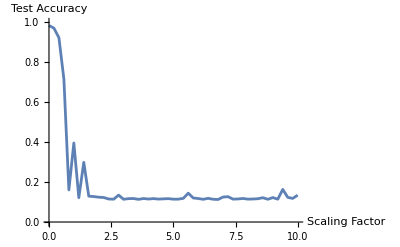

```mathematica
performancePlotLayer1Uniform=noisePerformancePlot[performanceListLayer1Uniform]
```

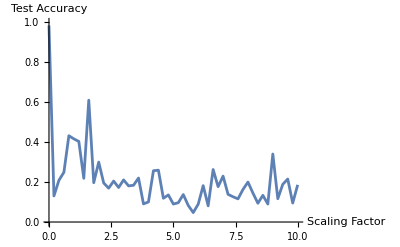

```mathematica
performancePlotLayer1Gaussian=noisePerformancePlot[performanceListLayer1Gaussian]
```

### Analysis

## Layer 4 (Convolutional Layer)

#### Uniform Distribution

```mathematica
performanceListLayer4Uniform=noisedNetPerformanceUniform[leNet,mnistTest,4,noiseRangeFactor]
```

#### Gaussian Distribution

```mathematica
performanceListLayer4Gaussian=noisedNetPerformanceGaussian[leNet,mnistTest,4,noiseRangeFactor]
```

### Visualization

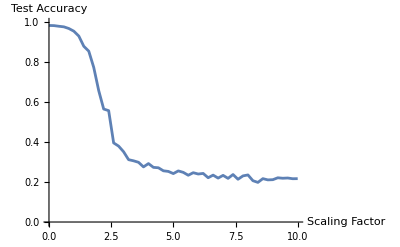

```mathematica
performancePlotLayer4Uniform=noisePerformancePlot[performanceListLayer4Uniform]
```

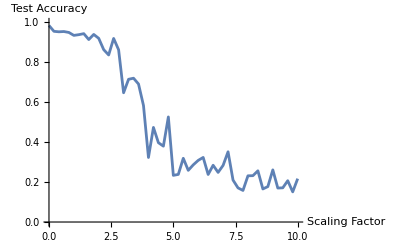

```mathematica
performancePlotLayer4Gaussian=noisePerformancePlot[performanceListLayer4Gaussian]
```

### Analysis

## Layer 8 (Linear Layer)

#### Uniform Distribution

```mathematica
performanceListLayer8Uniform=noisedNetPerformanceUniform[leNet,mnistTest,8,noiseRangeFactor]
```

#### Gaussian Distribution

```mathematica
performanceListLayer8Gaussian=noisedNetPerformanceGaussian[leNet,mnistTest,8,noiseRangeFactor]
```

### Visualization

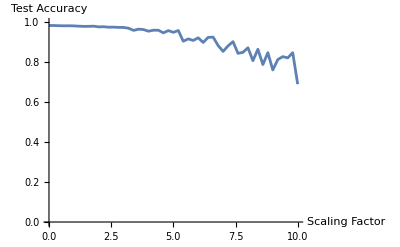

```mathematica
performancePlotLayer8Uniform=noisePerformancePlot[performanceListLayer8Uniform]
```

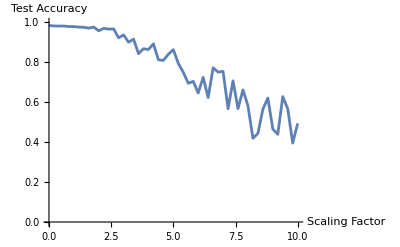

```mathematica
performancePlotLayer8Gaussian=noisePerformancePlot[performanceListLayer8Gaussian]
```

### Analysis

## Layer 10 (Linear Layer)

#### Uniform Distribution

```mathematica
performanceListLayer10Uniform=noisedNetPerformanceUniform[leNet,mnistTest,10,noiseRangeFactor]
```

#### Gaussian Distribution

```mathematica
performanceListLayer10Gaussian=noisedNetPerformanceGaussian[leNet,mnistTest,10,noiseRangeFactor]
```

### Visualization

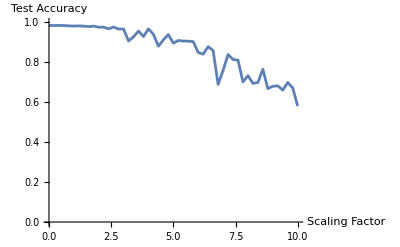

```mathematica
performancePlotLayer10Uniform=noisePerformancePlot[performanceListLayer10Uniform]
```

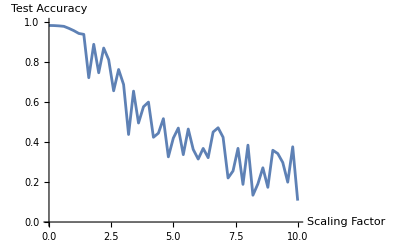

```mathematica
performancePlotLayer10Gaussian=noisePerformancePlot[performanceListLayer10Gaussian]
```

### Analysis

## 5. Discussion

- Degrade Continuously or Suddenly
- Types of confusion

- Layers

## 6. Confusion Matrix Analysis

Patterns?

### Layer 1

```mathematica
Table[performanceListLayer1Uniform[[n]][[3]],{n,Range[2,performanceListLayer1Uniform//Length]}]
```

```mathematica
Table[performanceListLayer1Gaussian[[n]][[3]],{n,Range[2,performanceListLayer1Gaussian//Length]}]
```

### Layer 4

```mathematica
Table[performanceListLayer4Uniform[[n]][[3]],{n,Range[2,performanceListLayer4Uniform//Length]}]
```

```mathematica
Table[performanceListLayer1Gaussian[[n]][[3]],{n,Range[2,performanceListLayer4Gaussian//Length]}]
```

### Layer 8

```mathematica
Table[performanceListLayer8Uniform[[n]][[3]],{n,Range[2,performanceListLayer8Uniform//Length]}]
```

```mathematica
Table[performanceListLayer1Gaussian[[n]][[3]],{n,Range[2,performanceListLayer8Gaussian//Length]}]
```

### Layer 10

```mathematica
Table[performanceListLayer10Uniform[[n]][[3]],{n,Range[2,performanceListLayer10Uniform//Length]}]
```

```mathematica
Table[performanceListLayer1Gaussian[[n]][[3]],{n,Range[2,performanceListLayer10Gaussian//Length]}]
```

## 7. Feature Representation Analysis

Why are the Convolutional Layers much more sensitive and susceptible to perturbations? In an attempt to answer this question, we investigate how the internal feature representation of a Convolutional Neural Network changes as a result of perturbing the weights with noise. A convolutional neural network like LeNet consists of two main parts: convolutional layers and fully connected layers. The main role of convolutional layers is to extract features from the input data for classification by the fully connected layers.

## Feature Map

In a convolutional neural network, a feature map basically refers to a single or the entire stack of channels of the output of a convolutional layer. It is learned representations of features in the spatial dimensions.3

LeNet has two convolutional layers, each with different output tensor size. the first and second convolutional layers have the dimensions of  and  respectively. 20 and 50 are the number of output channels and  and  are the output kernel size or the spatial resolution.

### Convolutional Layer 1

The first convolutional layer has an output of size   where 20 is  the number of output channels and  is the output kernel size or the spatial resolution.

```mathematica
NetExtract[leNet,1]
```

ConvolutionLayer[…]

### Convolutional Layer 2

The first convolutional layer has an output of size  where 50 is the number of output channels and  is the output kernel size or the spatial resolution.

```mathematica
NetExtract[leNet,4]
```

ConvolutionLayer[…]

We can observe that the first conv layer produces a feature map of a higher spatial resolution than the second conv layer while the second layer feature map has a fewer number of channels. This is typical of CNNs: the feature map of the first conv layer captures the basic patterns in the input image such as edges and lines while that of the conv second layer abstracts these patterns for classification.3

### Example: Feature Map

In this section, we observe how the LeNet’s power to represent the features of an image degrades as its weights are perturbed. We take one example from the test dataset of MNIST and feed it to both normal LeNet convolutional layers and the noised one. Then, we compare the visual feature map and observe how feature representation fails as the weights are noised.

#### Input

The LeNet takes an input image of size . Here, we take one arbitrary digit image and feed it into both the normal LeNet and the perturbed net.

```mathematica
inputImage=mnistTest[[7500]][[1]]
```

-Graphics-

```mathematica
inputMatrix=ImageData[inputImage];
```

#### 1st Layer (Convolution)

```mathematica
outputL1=NetExtract[leNet,1][ArrayReshape[inputMatrix,{1,28,28}]];
```

```mathematica
noisedWeights1= Normal[NetExtract[leNet,{1,"Weights"}]]+ RandomReal[{2*Quartiles[NetExtract[leNet,{1,"Weights"}]//Normal //Flatten][[1]],2*Quartiles[NetExtract[leNet,{1,"Weights"}]//Normal //Flatten][[3]]}, Dimensions[NetExtract[leNet,{1,"Weights"}]]];
```

```mathematica
outputL1Noised= NetExtract[NetReplacePart[leNet,{1,"Weights"}->NumericArray[noisedWeights1]],1][ArrayReshape[inputMatrix,{1,28,28}]]
```

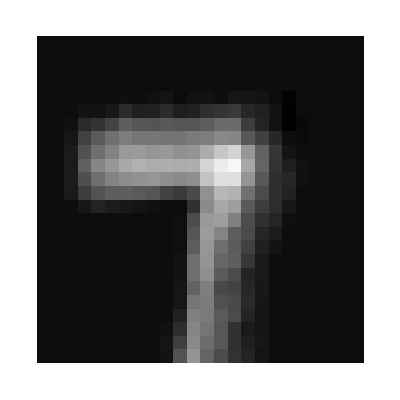
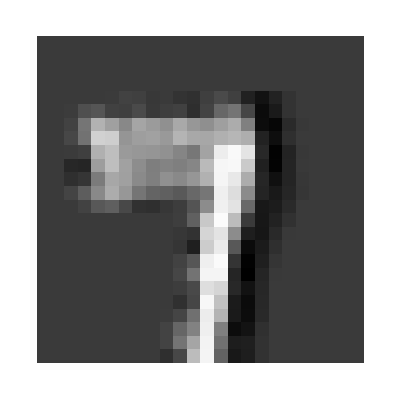
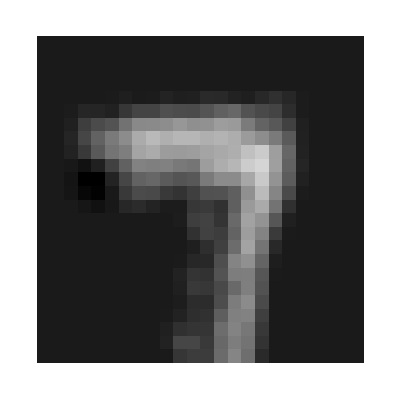
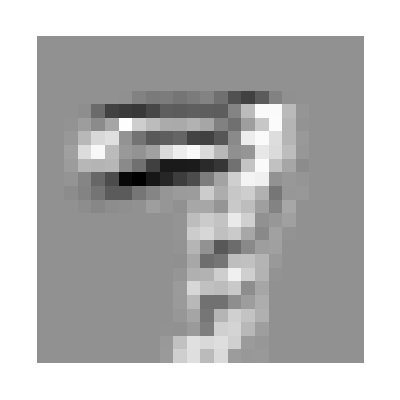
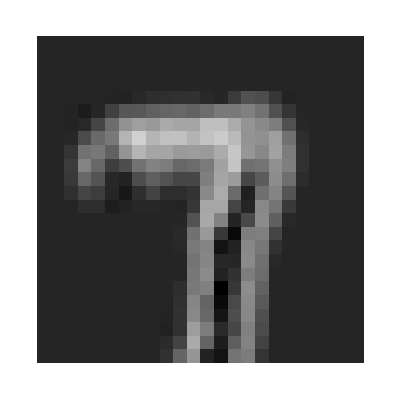
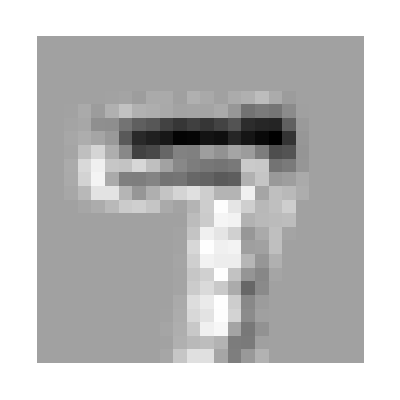
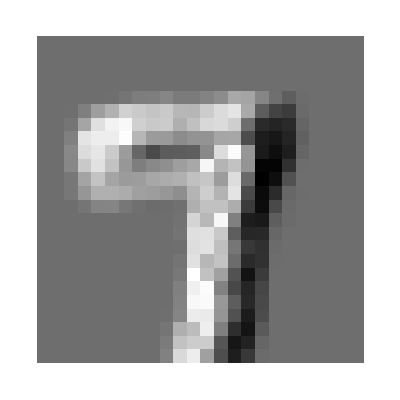
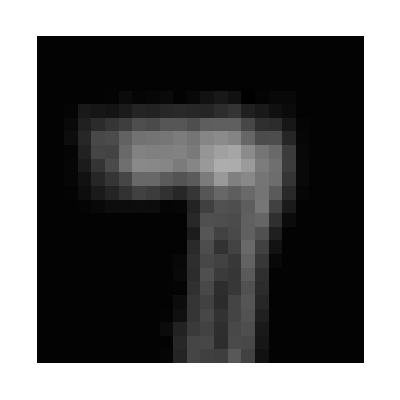
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{ArrayPlot/@ outputL1,ArrayPlot/@ outputL1Noised}]
```

#### 2nd Layer (ReLU)

```mathematica
outputL2=NetExtract[leNet,2][outputL1];
```

```mathematica
outputL2Noised=NetExtract[leNet,2][outputL1Noised]
```

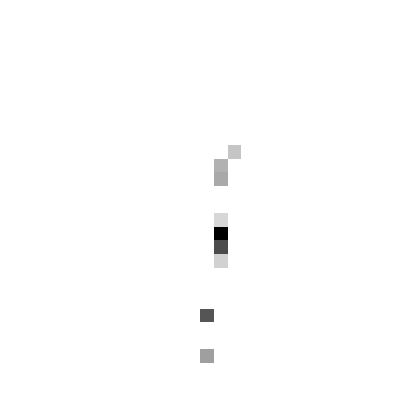
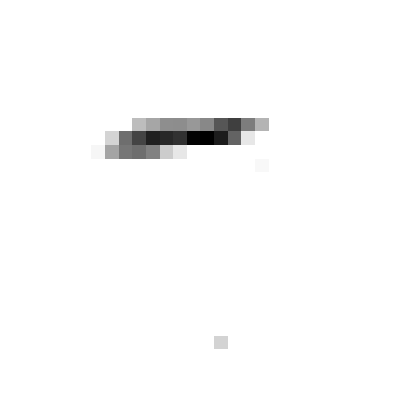
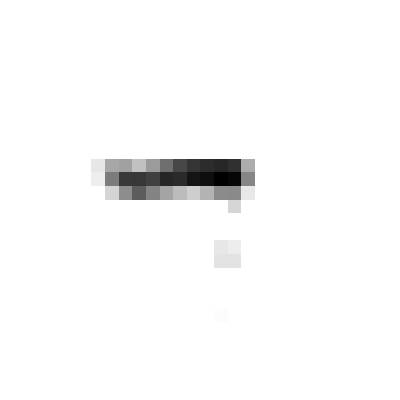
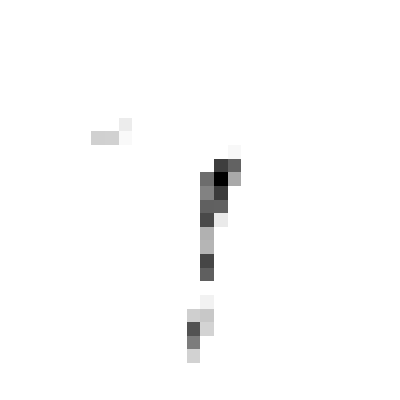
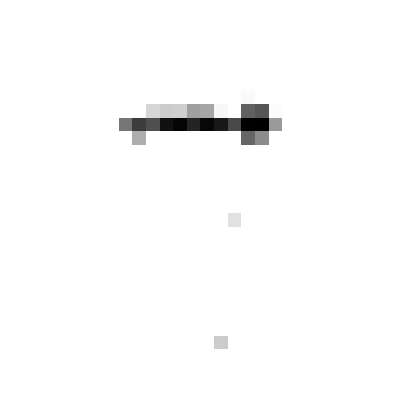
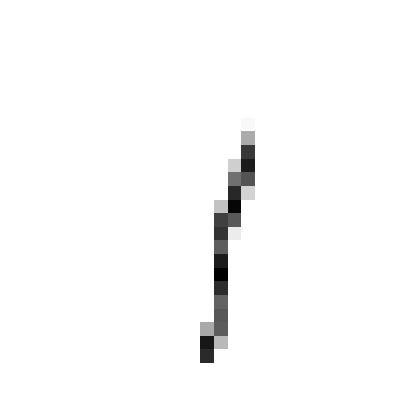
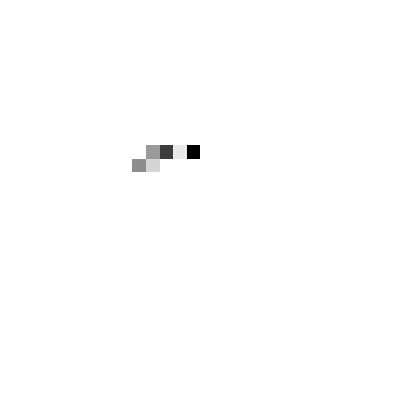
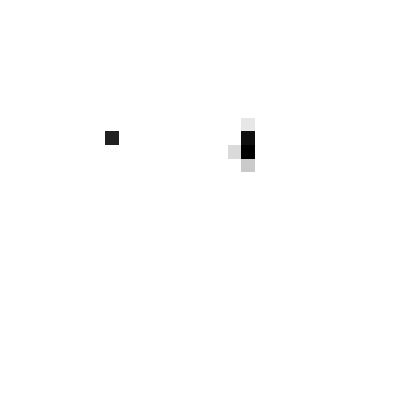
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{ArrayPlot/@outputL2,ArrayPlot/@outputL2Noised}]
```

#### 3rd Layer (Pooling)

```mathematica
outputL3=NetExtract[leNet,3][outputL2];
```

```mathematica
outputL3Noised=NetExtract[leNet,3][outputL2Noised];
```

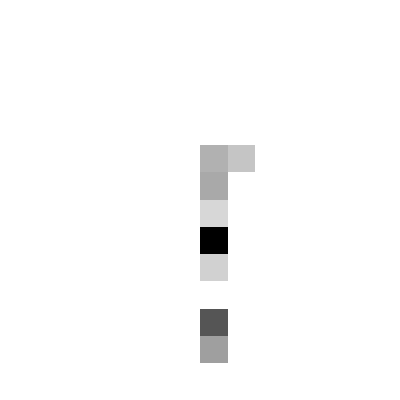
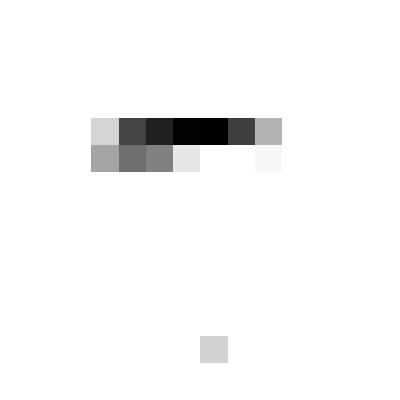
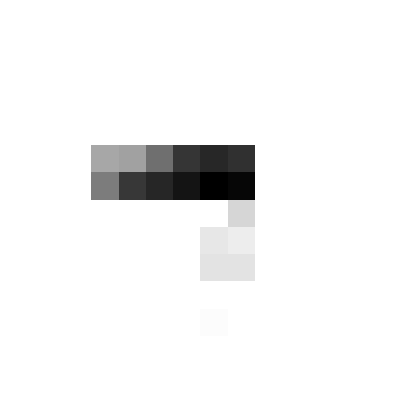
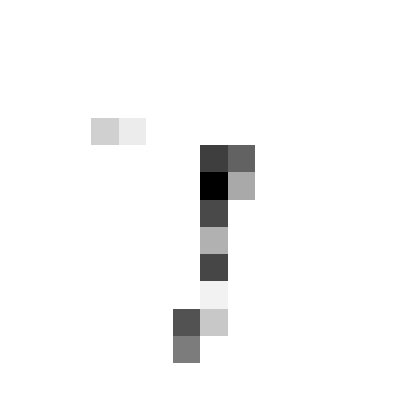
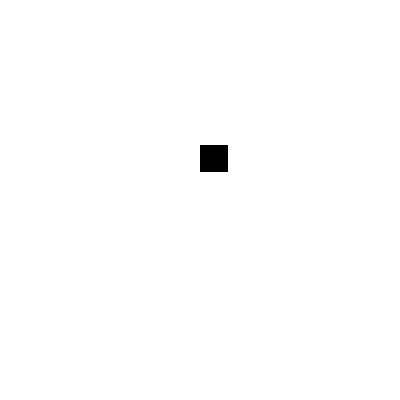
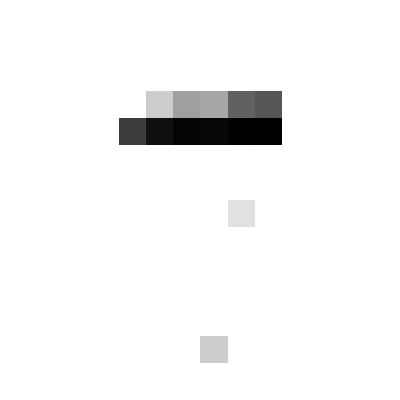
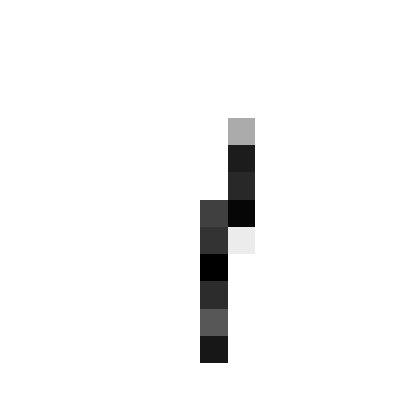
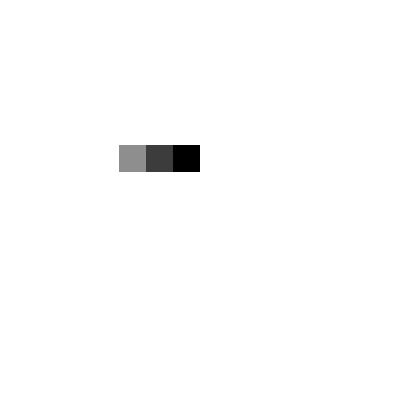
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{ArrayPlot/@outputL3,ArrayPlot/@outputL3Noised}]
```

#### 4th Layer (Convolution)

```mathematica
outputL4=NetExtract[leNet,4][outputL3];
```

```mathematica
outputL4Noised=NetExtract[leNet,4][outputL3Noised];
```

```mathematica
Grid[{ArrayPlot/@ outputL4,ArrayPlot/@ outputL4Noised}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### 5th Layer (ReLU)

```mathematica
outputL5=NetExtract[leNet,5][outputL4];
```

```mathematica
outputL5Noised=NetExtract[leNet,5][outputL4Noised];
```

```mathematica
Grid[{ArrayPlot/@ outputL5,ArrayPlot/@ outputL5Noised}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### 6th Layer (Pooling)

```mathematica
outputL6=NetExtract[leNet,6][outputL5];
```

```mathematica
outputL6Noised=NetExtract[leNet,6][outputL5Noised];
```

```mathematica
Grid[{ArrayPlot/@ outputL6,ArrayPlot/@ outputL6Noised}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### 7th~10th Layer (Fully Connected)

```mathematica
fullyConnceted=NetChain[Table[NetExtract[leNet,n],{n,{7,8,9,10,11}}]]
```

NetChain[<5>]

```mathematica
fullyConnceted[outputL6]//NetDecoder[{"Class",{0,1,2,3,4,5,6,7,8,9}}]
```

7

```mathematica
fullyConnceted[outputL6Noised]//NetDecoder[{"Class",{0,1,2,3,4,5,6,7,8,9}}]
```

1

## Feature Space

Above was an investigation of the change in feature map in a single example of a digit image. In this section, we investigate the entire feature space and how it shifts as the weights are perturbed.

```mathematica
performanceListLayer10Uniform//Length
```

6

```mathematica
performanceListLayer10Uniform//Dimensions
```

{6,2}

```mathematica
performanceListLayer10Uniform[[All,2]]
```

```mathematica
performanceListLayer10Uniform[[1]]//Dimensions
```

{2}

```mathematica
performanceListLayer10Uniform[[1]][[1]]//Dimensions
```

{}

```mathematica
performanceListLayer10Uniform[[1]][[2]]//Dimensions
```

{100}

```mathematica
performanceListLayer10Uniform[[1]][[2]][[1]]//Dimensions
```

{2}

```mathematica
performanceListLayer10Uniform[[1]][[2]][[1]][[1]]//Dimensions
```

{50,4,4}

```mathematica
Dimensions[fullData]
```

{6,100}

```mathematica
dimensionReducer=DimensionReduction[Keys@First[fullData]]
```

DimensionReducerFunction[…]

```mathematica
featureSpace[featureMap_List]:=Module[{dimensionReducer, },


dimensionReducer=DimensionsReduction[]
]
```

```mathematica
Manipulate[Module[
{data=Values[GroupBy[Thread[dimensionReducer[Keys[fullData[[idx]]]]->Values[fullData[[idx]]]],Values]]},
ListPlot[Keys/@data,PlotRange->{{-10,10},{-10,10}},PlotLegends->Values[First/@data]]
],{idx,1,Length[fullData],1}]
```

### Layer 1

### Layer 4

### Layer 8

### Layer 10

## 7. Conclusion

## 8. Future Work

## References

1	Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998)

2	LeCun, Y., Cortes, C. and Burges, C.J.C. (1998) The MNIST Database of Handwritten Digits. New York, USA. http://yann.lecun.com/exdb/mnist/

3	Torralba, A., Isola, P., & Freeman, W. T. (2024). Foundations of Computer Vision. The MIT Press.

Code Generated by ChatGPT 4-0
https://colab.research.google.com/drive/1MUbZSJMHj9rr9ORiA73aypDBjkHLS2Zs?usp=sharing